```mathematica
SetDirectory["/home/vsvh/docs/GMU/research/commpatterns/data"]
```

/home/vsvh/docs/GMU/research/commpatterns/data

```mathematica
ResourceFunction["MaTeXInstall"][]
```

PacletObject[…]

```mathematica
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12}
```

{FontFamily→Latin Modern Roman,FontSize→12}

```mathematica
data = Import["contour.dat"]
```

{{1,0,1.},{1,10,1.},{1,20,1.},{1,30,1.},{1,40,0.848765},{1,50,0.725309},{1,60,0.615741},{1,70,0.584877},{1,80,0.544753},{1,90,0.506173},{1,100,0.481481},{1,110,0.447531},{1,120,0.41821},{1,130,0.376543},{1,140,0.337963},{1,150,0.291667},{1,160,0.223765},{1,170,0.166667},{1,180,0.118827},{1,190,0.070988},{1,200,0.007716},{2,0,1.},{2,10,1.},{2,20,1.},{2,30,1.},{2,40,0.919105},{2,50,0.824441},{2,60,0.736661},{2,70,0.703959},{2,80,0.667814},{2,90,0.636833},{2,100,0.593804},{2,110,0.569707},{2,120,0.521515},{2,130,0.444062},{2,140,0.383821},{2,150,0.321859},{2,160,0.251291},{2,170,0.185886},{2,180,0.134251},{2,190,0.079174},{2,200,0.008606},{4,0,1.},{4,10,1.},{4,20,1.},{4,30,1.},{4,40,0.958237},{4,50,0.911833},{4,60,0.837587},{4,70,0.791183},{4,80,0.767981},{4,90,0.726218},{4,100,0.682135},{4,110,0.663573},{4,120,0.645012},{4,130,0.584687},{4,140,0.515081},{4,150,0.450116},{4,160,0.37355},{4,170,0.264501},{4,180,0.167053},{4,190,0.090487},{4,200,0.018561},{8,0,1.},{8,10,1.},{8,20,1.},{8,30,1.},{8,40,0.990476},{8,50,0.957143},{8,60,0.890476},{8,70,0.852381},{8,80,0.828571},{8,90,0.8},{8,100,0.771429},{8,110,0.742857},{8,120,0.714286},{8,130,0.7},{8,140,0.638095},{8,150,0.580952},{8,160,0.452381},{8,170,0.252381},{8,180,0.157143},{8,190,0.104762},{8,200,0.004762},{16,0,1.},{16,10,1.},{16,20,1.},{16,30,1.},{16,40,0.98913},{16,50,0.956522},{16,60,0.934783},{16,70,0.902174},{16,80,0.880435},{16,90,0.869565},{16,100,0.847826},{16,110,0.826087},{16,120,0.804348},{16,130,0.76087},{16,140,0.728261},{16,150,0.684783},{16,160,0.565217},{16,170,0.402174},{16,180,0.271739},{16,190,0.173913},{16,200,0.043478},{32,0,1.},{32,10,1.},{32,20,1.},{32,30,1.},{32,40,0.970588},{32,50,0.941176},{32,60,0.941176},{32,70,0.941176},{32,80,0.882353},{32,90,0.852941},{32,100,0.794118},{32,110,0.794118},{32,120,0.794118},{32,130,0.794118},{32,140,0.705882},{32,150,0.676471},{32,160,0.647059},{32,170,0.5},{32,180,0.264706},{32,190,0.147059},{32,200,0.058824}}

```mathematica
{{0,0,1.},{0,1,1.},{0,2,1.},{0,3,1.},{0,4,0.848765},{0,5,0.725309},{0,6,0.615741},{0,7,0.584877},{0,8,0.544753},{0,9,0.506173},{0,10,0.481481},{0,11,0.447531},{0,12,0.41821},{0,13,0.376543},{0,14,0.337963},{0,15,0.291667},{0,16,0.223765},{0,17,0.166667},{0,18,0.118827},{0,19,0.070988},{0,20,0.007716},{1,0,1.},{1,1,1.},{1,2,1.},{1,3,1.},{1,4,0.919105},{1,5,0.824441},{1,6,0.736661},{1,7,0.703959},{1,8,0.667814},{1,9,0.636833},{1,10,0.593804},{1,11,0.569707},{1,12,0.521515},{1,13,0.444062},{1,14,0.383821},{1,15,0.321859},{1,16,0.251291},{1,17,0.185886},{1,18,0.134251},{1,19,0.079174},{1,20,0.008606},{2,0,1.},{2,1,1.},{2,2,1.},{2,3,1.},{2,4,0.958237},{2,5,0.911833},{2,6,0.837587},{2,7,0.791183},{2,8,0.767981},{2,9,0.726218},{2,10,0.682135},{2,11,0.663573},{2,12,0.645012},{2,13,0.584687},{2,14,0.515081},{2,15,0.450116},{2,16,0.37355},{2,17,0.264501},{2,18,0.167053},{2,19,0.090487},{2,20,0.018561},{3,0,1.},{3,1,1.},{3,2,1.},{3,3,1.},{3,4,0.990476},{3,5,0.957143},{3,6,0.890476},{3,7,0.852381},{3,8,0.828571},{3,9,0.8},{3,10,0.771429},{3,11,0.742857},{3,12,0.714286},{3,13,0.7},{3,14,0.638095},{3,15,0.580952},{3,16,0.452381},{3,17,0.252381},{3,18,0.157143},{3,19,0.104762},{3,20,0.004762},{4,0,1.},{4,1,1.},{4,2,1.},{4,3,1.},{4,4,0.98913},{4,5,0.956522},{4,6,0.934783},{4,7,0.902174},{4,8,0.880435},{4,9,0.869565},{4,10,0.847826},{4,11,0.826087},{4,12,0.804348},{4,13,0.76087},{4,14,0.728261},{4,15,0.684783},{4,16,0.565217},{4,17,0.402174},{4,18,0.271739},{4,19,0.173913},{4,20,0.043478}}
```

```mathematica
points0 = Import["points0.dat"];
points1 = Import["points1.dat"];
points2 = Import["points2.dat"];
points3 = Import["points3.dat"]
```

{{1,0},{1,10},{1,20},{1,30},{1,40},{2,0},{2,10},{2,20},{2,30},{2,40},{2,50},{2,60},{3,0},{3,10},{3,20},{3,30},{3,40},{3,50},{3,60},{3,70},{3,80},{4,0},{4,10},{4,20},{4,30},{4,40},{4,50},{4,60},{4,70},{4,80},{4,90},{5,0},{5,10},{5,20},{5,30},{5,40},{5,50},{5,60},{5,70},{5,80},{5,90},{5,100},{5,110},{5,120},{5,130},{6,0},{6,10},{6,20},{6,30},{6,40},{6,50},{6,60},{6,70},{6,80},{6,90},{6,100},{6,110},{6,120},{7,0},{7,10},{7,20},{7,30},{7,40},{7,50},{7,60},{7,70},{7,80},{7,90},{7,100},{7,110},{8,0},{8,10},{8,20},{8,30},{8,40},{8,50},{8,60},{8,70},{8,80},{8,90},{8,100},{8,110},{9,0},{9,10},{9,20},{9,30},{9,40},{9,50},{10,0},{10,10},{10,20},{10,30},{10,40},{10,50},{10,60},{10,70},{10,80},{10,90},{10,100},{10,110},{11,0},{11,10},{11,20},{11,30},{11,40},{11,50},{11,60},{11,70},{11,80},{11,90},{11,100},{11,110},{11,120},{11,130},{11,140},{12,0},{12,10},{12,20},{12,30},{12,40},{12,50},{12,60},{12,70},{13,0},{13,10},{13,20},{13,30},{13,40},{13,50},{13,60},{13,70},{13,80},{13,90},{14,0},{14,10},{14,20},{14,30},{14,40},{14,50},{14,60},{14,70},{14,80},{14,90},{14,100},{14,110},{14,120},{14,130},{14,140},{15,0},{15,10},{15,20},{15,30},{15,40},{15,50},{15,60},{15,70},{15,80},{15,90},{15,100},{15,110},{15,120},{15,130},{15,140},{15,150},{15,160},{15,170},{16,0},{16,10},{16,20},{16,30},{16,40},{16,50},{16,60},{16,70},{16,80},{16,90},{16,100},{16,110},{17,0},{17,10},{17,20},{17,30},{17,40},{17,50},{17,60},{17,70},{17,80},{17,90},{17,100},{17,110},{17,120},{17,130},{18,0},{18,10},{18,20},{18,30},{18,40},{18,50},{18,60},{18,70},{18,80},{18,90},{18,100},{18,110},{18,120},{18,130},{19,0},{19,10},{19,20},{19,30},{19,40},{19,50},{19,60},{19,70},{19,80},{19,90},{19,100},{19,110},{19,120},{19,130},{19,140},{19,150},{19,160},{21,0},{21,10},{21,20},{21,30},{21,40},{21,50},{21,60},{21,70},{21,80},{21,90},{21,100},{21,110},{21,120},{21,130},{21,140},{22,0},{22,10},{22,20},{22,30},{22,40},{22,50},{22,60},{22,70},{22,80},{22,90},{22,100},{22,110},{22,120},{22,130},{22,140},{22,150},{22,160},{22,170},{25,0},{25,10},{25,20},{25,30},{25,40},{33,0},{33,10},{33,20},{33,30},{33,40},{33,50},{33,60},{33,70},{33,80},{33,90},{33,100},{33,110},{33,120},{33,130},{33,140},{33,150},{33,160}}

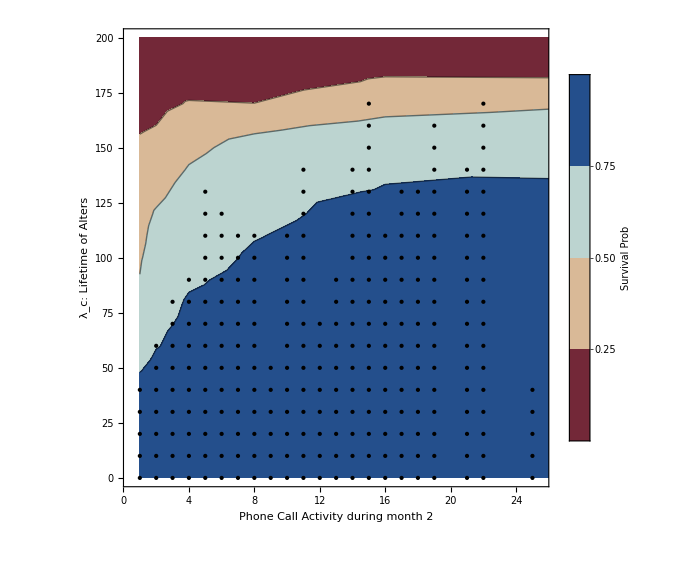

```mathematica
pc = ListContourPlot[data,BaseStyle->texStyle, PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Survival Prob",LabelStyle->{ FontFamily->"Latin Modern Roman", FontSize->20}],Right], FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->18}, ImageSize->Large, ColorFunction->"RedBlueTones", Contours->3, ScalingFunctions->{None, None}, PlotRange->{{0.5, 25.5}, Full}, Epilog->{PointSize[Large],Black,Point[points3]}]
```

```mathematica
marker0 = Graphics[{EdgeForm[Thickness[0.2]],ColorData["RedBlueTones"][0], Disk[]}];
marker1 = Graphics[{EdgeForm[Thickness[0.2]],ColorData["RedBlueTones"][0.3], Disk[]}];
marker2 = Graphics[{EdgeForm[Thickness[0.2]],ColorData["RedBlueTones"][0.6], Disk[]}];
marker3 = Graphics[{EdgeForm[Thickness[0.2]],ColorData["RedBlueTones"][0.99], Disk[]}];
```

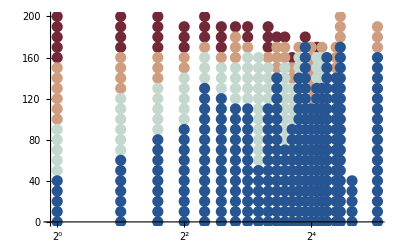

```mathematica
a = ListPlot[{points0, points1, points2, points3}, BaseStyle->texStyle, PlotMarkers->{{marker0, 0.02}, {marker1, 0.02}, {marker2, 0.02}, {marker3, 0.02}}, ScalingFunctions->{"Log2", None}]
```

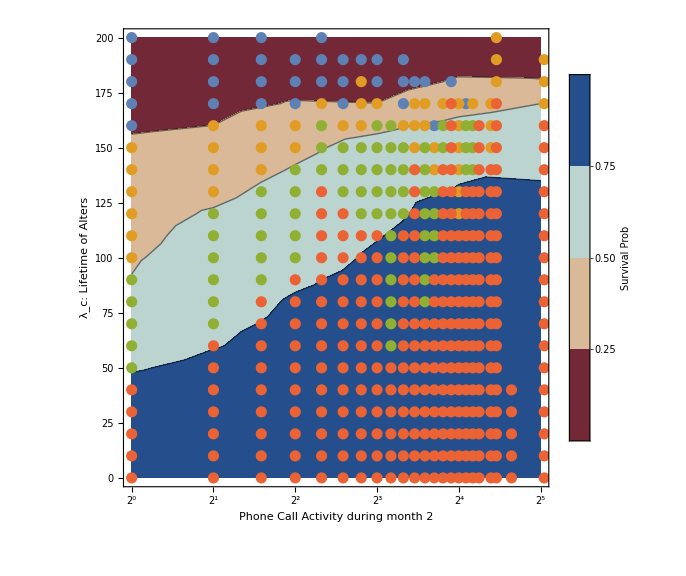

```mathematica
plot = Show[pc, a]
```

```mathematica
Export["../img/contour.pdf", plot]
```

../img/contour.pdf

```mathematica
ColorData["Gradients"][1]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}[1]

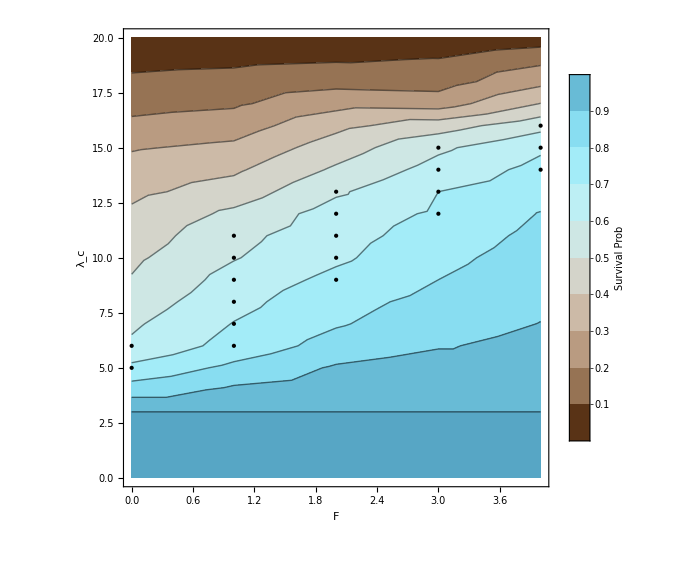

```mathematica
ListContourPlot[data,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Survival Prob",LabelStyle->{ Italic,FontFamily->"Helvetica", FontSize->20}],Right], FrameLabel->{"F","\[\Lambda]_c"}, LabelStyle->{FontFamily->"Helvetica", FontSize->18}, ImageSize->Large, ColorFunction->"BrownCyanTones", Epilog->{PointSize[Large],Black,Point[points3]}]
```

```mathematica
$FontFamilies
```

{Alegreya SC,all-the-icons,Andale Mono,Apple Garamond,Apple Garamond Light,Arial,Arial Black,Bitstream Charter,Bitstream Vera Sans,Bitstream Vera Sans Mono,Bitstream Vera Serif,C059,Cantarell,Cantarell Extra Bold,Cantarell Light,Cantarell Thin,Clear Sans,Clear Sans Light,Clear Sans Medium,Clear Sans Thin,Comic Sans MS,Courier,Courier New,Cousine,D050000L,Droid Serif,EB Garamond,EB Garamond 08,EB Garamond 12 All SC,EB Garamond SC,EB Garamond SC 08,Economica,Felipa,file-icons,Fira Sans,Fira Sans Book,Fira Sans Compressed,Fira Sans Compressed Book,Fira Sans Compressed Eight,Fira Sans Compressed ExtraBold,Fira Sans Compressed ExtraLight,Fira Sans Compressed Four,Fira Sans Compressed Hair,Fira Sans Compressed Heavy,Fira Sans Compressed Light,Fira Sans Compressed Medium,Fira Sans Compressed SemiBold,Fira Sans Compressed Thin,Fira Sans Compressed Two,Fira Sans Compressed UltraLight,Fira Sans Condensed,Fira Sans Condensed Book,Fira Sans Condensed Eight,Fira Sans Condensed ExtraBold,Fira Sans Condensed ExtraLight,Fira Sans Condensed Four,Fira Sans Condensed Hair,Fira Sans Condensed Heavy,Fira Sans Condensed Light,Fira Sans Condensed Medium,Fira Sans Condensed SemiBold,Fira Sans Condensed Thin,Fira Sans Condensed Two,Fira Sans Condensed UltraLight,Fira Sans Eight,Fira Sans ExtraBold,Fira Sans ExtraLight,Fira Sans Four,Fira Sans Hair,Fira Sans Heavy,Fira Sans Light,Fira Sans Medium,Fira Sans SemiBold,Fira Sans Thin,Fira Sans Two,Fira Sans Ultra,Fira Sans UltraLight,FontAwesome,Font Awesome 5 Brands,Font Awesome 5 Free,FreeMono,FreeSans,FreeSerif,Gentium Basic,Georgia,github-octicons,Hard Gothic,Hasklig,Hasklig Black,Hasklig ExtraLight,Hasklig Light,Hasklig Medium,Hasklig Semibold,Impact,Inconsolata,JoyPixels,Kalam,Kalam Bold,Kalam Light,Lato,Lato Black,Lato Hairline,Lato Light,League Gothic,League Gothic Condensed,League Gothic Condensed Italic,Liberation Mono,Liberation Sans,Liberation Serif,Lucida Console,Lucida G,Lucida Gr,Lucida Grande,LucidaMacBold,Lucida MAC [PfEd],Lucida MAC [unknown],Lucida Sans Unicode,MACGrande,Material Icons,Mathematica,MathematicaMono,MathematicaSans,Meslo LG L,Meslo LG L DZ,Meslo LG M,Meslo LG M DZ,Meslo LG S,Meslo LG S DZ,MesloLGS NF,Monospace,Nimbus Mono PS,Nimbus Roman,Nimbus Sans Narrow,Nimbus Sans [UKWN],Nimbus Sans [URW ],Oswald,P052,Playfair Display,Playfair Display Black,Roboto,Roboto Black,Roboto Condensed,Roboto Condensed Light,Roboto Light,Roboto Medium,Roboto Slab,Roboto Thin,Sans Serif,Serif,Shadows Into Light Two,Source Code Pro,Source Code Pro Black,Source Code Pro ExtraLight,Source Code Pro Light,Source Code Pro Medium,Source Code Pro Semibold,Source Code Variable,Source Sans Pro,Source Sans Pro Black,Source Sans Pro ExtraLight,Source Sans Pro Light,Source Sans Pro SemiBold,Source Serif Pro,Source Serif Pro Semibold,Standard Symbols PS,Swiss 721,Times New Roman,Titillium Web,Trebuchet MS,Twitter Color Emoji,URW Bookman,URW Gothic,Utopia,Verdana,Weather Icons,Webdings,WolframModern,Yanone Kaffeesatz,Yanone Kaffeesatz Extra Light,Yanone Kaffeesatz Light,Z003}

```mathematica
data2 = Import["contour2.dat"];
```

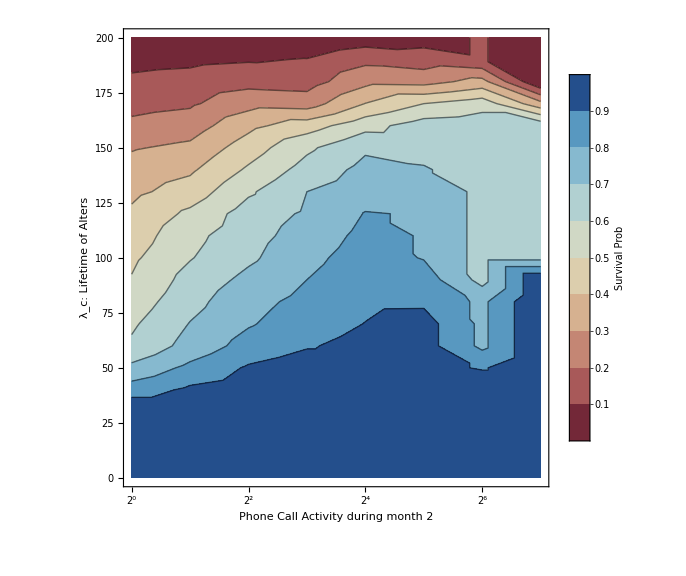

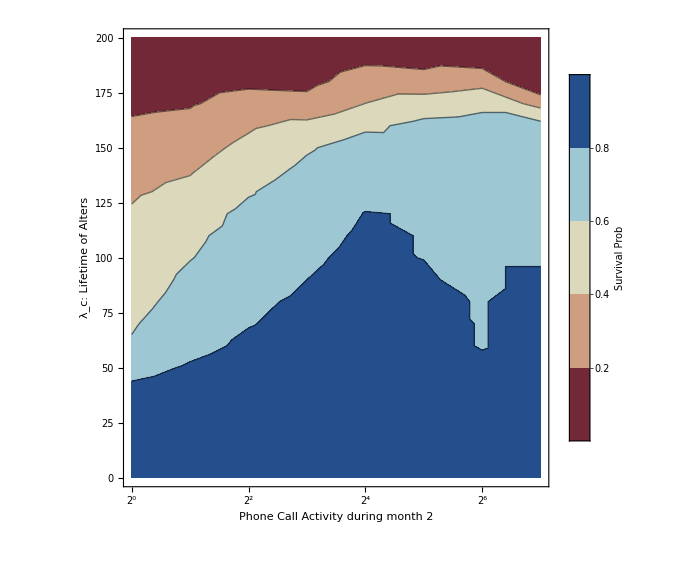

```mathematica
pc2 = ListContourPlot[data2,BaseStyle->texStyle, PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Survival Prob",LabelStyle->{ FontFamily->"Latin Modern Roman", FontSize->20}],Right], FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->18}, ImageSize->Large, ColorFunction->"RedBlueTones", Contours->9, ScalingFunctions->{"Log2", None}]
```

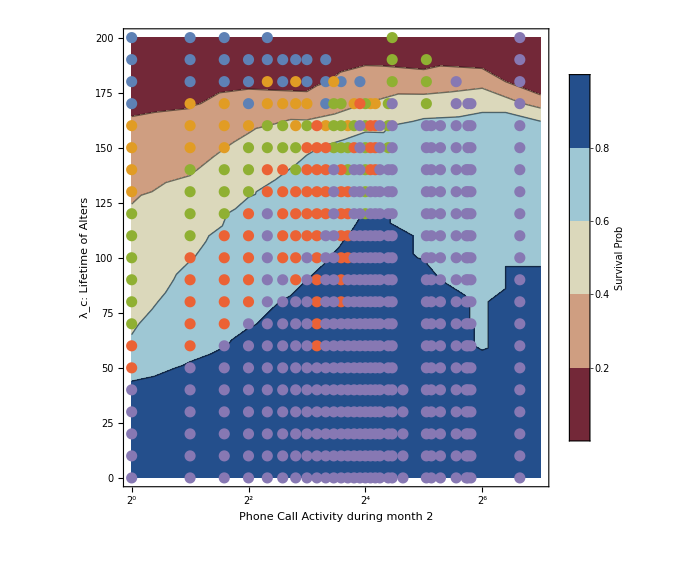

```mathematica
plot = Show[pc2, a]
```

```mathematica
thebar = BarLegend[{"RedBlueTones",{0,1}},3, LegendLabel->"Survival Prob.", LabelStyle->{FontSize->12, FontFamily->"Latin Modern Roman"}, LegendFunction->Framed, LegendMarkerSize->300, LegendLayout->"Row"]
```

```mathematica
pp0 = ListPlot[points0,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}];
pp1 = ListPlot[points1,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}];
pp2 = ListPlot[points2,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}];
pp3 = ListPlot[points3,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}];
```

```mathematica
p11 = ListContourPlot[data,BaseStyle->texStyle, FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Automatic, ColorFunction->"RedBlueTones", Contours->3, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}];
p12 = ListContourPlot[data,BaseStyle->texStyle, FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Automatic, ColorFunction->"RedBlueTones", Contours->3, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}];
p21 = ListContourPlot[data,BaseStyle->texStyle, FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Automatic, ColorFunction->"RedBlueTones", Contours->3, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}];
p22 = ListContourPlot[data,BaseStyle->texStyle,FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Automatic, ColorFunction->"RedBlueTones", Contours->3, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}];
```

```mathematica
g11 = Show[p11, pp0];
g12 = Show[p12, pp1];
g21 = Show[p21, pp2];
g22 = Show[p22, pp3];
```

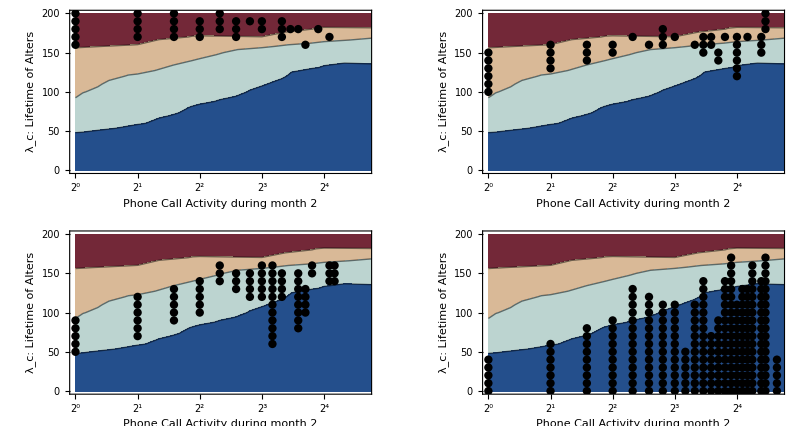

```mathematica
grid = GraphicsGrid[{{g11, g12}, {g21, g22}, {thebar, SpanFromLeft}}, ImageSize->Full]
```

```mathematica
grid
```

-Graphics-

```mathematica
Export["/home/vsvh/back/grid.pdf",%376,"PDF"]
```

/home/vsvh/back/grid.pdf

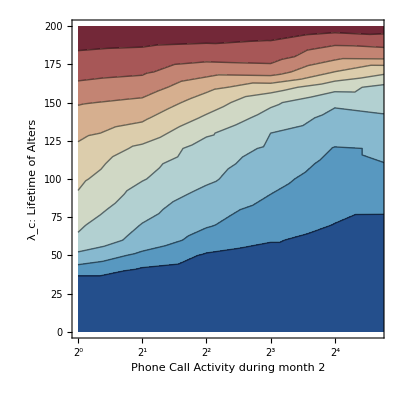

```mathematica
a = ListContourPlot[data,BaseStyle->texStyle,FrameLabel->{"Phone Call Activity during month 2","\[\Lambda]_c: Lifetime of Alters"}, LabelStyle->{FontSize->12}, ImageSize->Automatic, ColorFunction->"RedBlueTones", Contours->9, ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}]
```

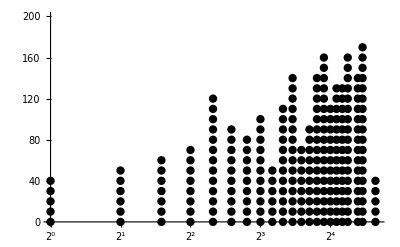

```mathematica
b = ListPlot[points4,ScalingFunctions->{"Log2", None}, PlotRange->{{1, 25.5}, Full}, PlotStyle->{PointSize[0.015], Black}]
```

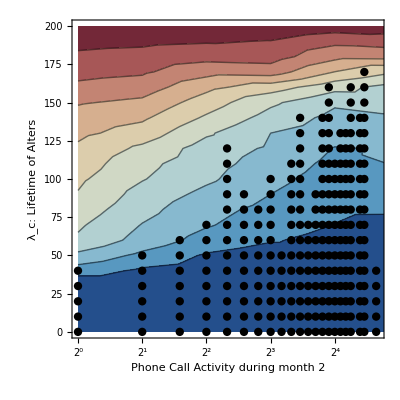

```mathematica
Show[a, b]
```